```mathematica
α=0.01;m=10;
Get["C:\\Users\\ASUS\\Documents\\SyntheticPotential_"<>"Alpha="<>ToString[α]<>"&m="<>ToString[m]<>".ex"]
```

```mathematica
aa={100,10,5,1,0.5,0.1,0.01,0.005(*,0.001*)};
```

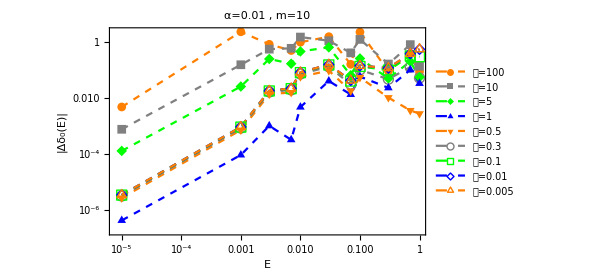

C:\Users\ASUS\OneDrive\Documents\Test_6\Test_Determine_a_Alpha=0.01&m=10.eps

```mathematica
ListLogLogPlot[Table[La[[n]],{n,Length@aa}],Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->450,FrameLabel->{"E","|Δδ_0(E)|"},(*RotateLabel->False,*)PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}},PlotLegends->Placed[LineLegend[(("𝒶="<>ToString[#])&/@aa),LegendLayout->{"Column",2}(*,LegendMarkerSize->20*),LegendMargins->{{0,0},{0,0}}(*,LegendFunction->Framed*)],(*{{},{}}*){Right,Bottom}],PlotLabel->Style[("α="<>ToString@α<>" ,  m="<>ToString@m),18],FrameTicksStyle->{Bold,12}]
Evaluate["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\Test_Determine_a_Alpha="<>ToString[α]<>"&m="<>ToString[m]<>".eps"]
(*Export[%,%%];*)
```

```mathematica
TableForm[Partition[#,IntegerPart@((Length@aa)/4)]]&[(("𝒶="<>ToString[#])&/@aa)]
```

𝒶=100 | 𝒶=10
𝒶=5 | 𝒶=1
𝒶=0.5 | 𝒶=0.3
𝒶=0.1 | 𝒶=0.01

```mathematica
LineLegend[(("𝒶="<>ToString[#])&/@aa),LegendLayout->TableForm[Partition[#,IntegerPart@((Length@aa)/4)]]&]
```

LineLegend[{𝒶=100,𝒶=10,𝒶=5,𝒶=1,𝒶=0.5,𝒶=0.3,𝒶=0.1,𝒶=0.01,𝒶=0.005},LegendLayout→Partition[#1,IntegerPart[Length[aa]/4]]&]